```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v2/datav4

```mathematica
dataall=Table[Import["./Shi_700-870_band=15_nodes=21/Shi_mu="<>ToString[i]<>"_m0=700.0-flag_4-21x120_VC=true.csv"],{i,800,870,5}];
```

```mathematica
n=Length[Table[i,{i,800,870,5}]]
```

15

```mathematica
dataall[[1]]
```

```mathematica
pdata=Table[Table[Table[dataall[[n1]][[j*120+i]][[5]],{i,2,121}],{j,0,20}],{n1,1,15}];
```

```mathematica
Table[Table[Export["./mub"<>ToString[(i-1)*5+800]<>"/V"<>ToString[j]<>".dat",pdata[[i]][[j]]],{i,1,15}],{j,1,21}];
```

```mathematica
T=Table[i,{i,1,120}];
```

```mathematica
Length[pdata[[1]]]
```

51

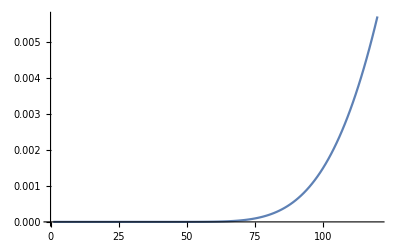

```mathematica
ListLinePlot[pdata[[1]][[10]]*197.33^3/T^4,PlotRange->All]
```